```mathematica
Multicolumn[Table[If[PrimeQ[n],Framed[Style[n, Red]], n], {n,1,70}],{10,7}]
```

1 | 11 | 21 | 31 | 41 | 51 | 61
2 | 12 | 22 | 32 | 42 | 52 | 62
3 | 13 | 23 | 33 | 43 | 53 | 63
4 | 14 | 24 | 34 | 44 | 54 | 64
5 | 15 | 25 | 35 | 45 | 55 | 65
6 | 16 | 26 | 36 | 46 | 56 | 66
7 | 17 | 27 | 37 | 47 | 57 | 67
8 | 18 | 28 | 38 | 48 | 58 | 68
9 | 19 | 29 | 39 | 49 | 59 | 69
10 | 20 | 30 | 40 | 50 | 60 | 70

用 NextPrimepaclet:ref/NextPrime 绘制六角形质数螺旋：

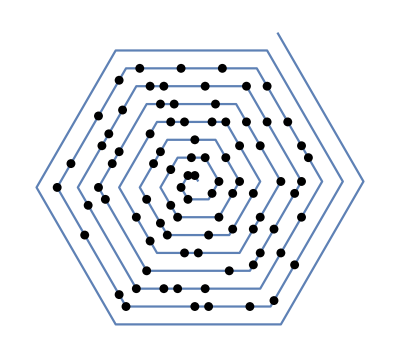

```mathematica
hexagonalSpiral[n_]:={Re[#],Im[#]}&/@Fold[Join[#1,Last[#1]+Exp[I Pi/3]^#2 Range[#2/2]]&,{0},Range[n]]
spiral=hexagonalSpiral[50];
nextprimes=spiral[[DeleteDuplicates[NextPrime[Range[PrimePi[5*Length[spiral]]]]]]];
ListPlot[spiral,Joined->True,Axes->False,AspectRatio->Automatic,Epilog->{PointSize[0.016],Point[nextprimes]}]
```

```mathematica
ulam[n_]:=Partition[Permute[Range[n^2],Accumulate[Take[Flatten[{{n^2+1}/2, Table
	[(-1)^j i,{j,n},{i,{-1,n}},{j}]}],n^2]]],n]
ulam[5]//TableForm
```

17 | 16 | 15 | 14 | 13
18 | 5 | 4 | 3 | 12
19 | 6 | 1 | 2 | 11
20 | 7 | 8 | 9 | 10
21 | 22 | 23 | 24 | 25

```mathematica
ulam[5]
```

{{17,16,15,14,13},{18,5,4,3,12},{19,6,1,2,11},{20,7,8,9,10},{21,22,23,24,25}}

```mathematica
LogIntegral[2]
```

LogIntegral[2]

```mathematica
N[LogIntegral[2]]
```

1.04516

```mathematica
Table[N[ZetaZero[k]],{k,5}]
```

{0.5+14.1347 ⅈ,0.5+21.022 ⅈ,0.5+25.0109 ⅈ,0.5+30.4249 ⅈ,0.5+32.9351 ⅈ}

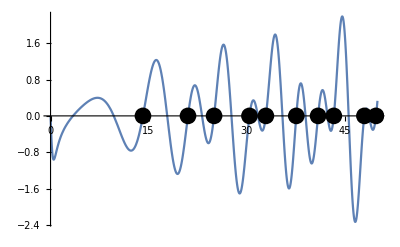

```mathematica
Plot[Im[Zeta[1/2+ⅈ z]],{z,0,50},Epilog->{PointSize[0.03],Point[Table[{Im[ZetaZero[k]],0},{k,10}]]}]
```

```mathematica
Series[Log[1+1/x],{x,0,3}]
```

Log[1/x]+x-x^2/2+x^3/3+O[x]^4

```mathematica
Reduce[NextPrime[x] -x==2&&0<x<20&&PrimeQ[x],x∈Integers]
```

False